### Filename

```mathematica
stell="WISTELL-A";
SetDirectory["/Users/rogeriojorge/Dropbox/PostDoc/Near Axis Gyrokinetics/GS2/"<>stell];
initialT=50;
filenameNA="gs2Input_"<>stell<>"r0.01.out.nc";
filenameX="gs2Input_"<>stell<>"r0.05.out.nc";
```

### Available Datasets

```mathematica
Import[filenameNA,{"Datasets"}]
```

{code_info,input_file,nproc,nmesh,nkx,nky,ntheta_tot,nspecies,nenergy,nlambda,aref,zref,nref,tref,lref,vref,bref,rhoref,charge,mass,dens,temp,tprim,fprim,uprim,uprim2,vnewk,type_of_species,t,theta0,kx,ky,egrid,lambda,theta,bmag,gradpar,gbdrift,gbdrift0,cvdrift,cvdrift0,cdrift,cdrift0,gds2,gds21,gds22,grho,jacob,q,eps,beta,shat,drhodpsi,phi,phi2,phi2_by_mode,phi0,es_heat_par,es_heat_perp,es_heat_flux,es_mom_flux,es_part_flux,es_exchange,es_exchange_by_k,es_heat_by_k,es_mom_by_k,es_part_by_k,es_parmom_by_k,es_perpmom_by_k,es_mom0_by_k,es_mom1_by_k,phi_norm,phase,phtot,hflux_tot,vflux_tot,zflux_tot,ntot,density,upar,tpar,tperp,qparflux,pperpj1,qpperpj1}

### Store data and fit

```mathematica
phiNA=Import[filenameNA,{"Datasets","phi"}][[1,1]];
phiX=Import[filenameX,{"Datasets","phi"}][[1,1]];
thetaNA=Import[filenameNA,{"Datasets","theta"}];
thetaX=Import[filenameX,{"Datasets","theta"}];
phi2NA=Import[filenameNA,{"Datasets","phi2"}];
phi2X=Import[filenameX,{"Datasets","phi2"}];
timeNA=Import[filenameNA,{"Datasets","t"}];
timeX=Import[filenameX,{"Datasets","t"}];
fitSolNA[x_]=Fit[Transpose@{timeNA[[initialT;;]],Log[phi2NA[[initialT;;]]]},{1,x},x];
fitSolX[x_]=Fit[Transpose@{timeX[[initialT;;]],Log[phi2X[[initialT;;]]]},{1,x},x];
gammaNA=ToString@D[fitSolNA[x],x];
gammaX=ToString@D[fitSolX[x],x];
```

### Plot

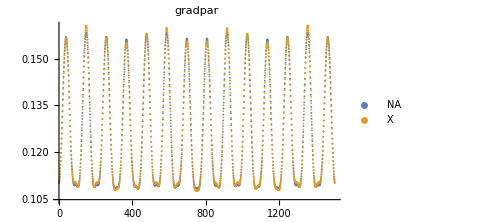
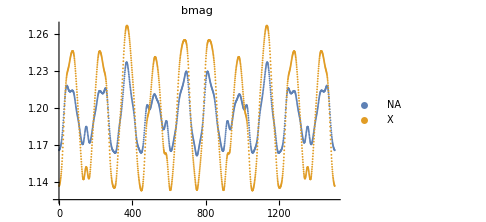
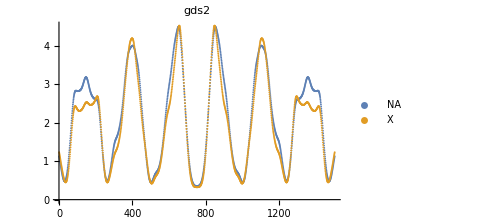
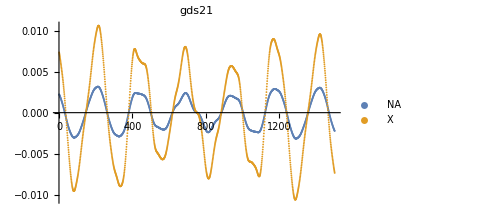
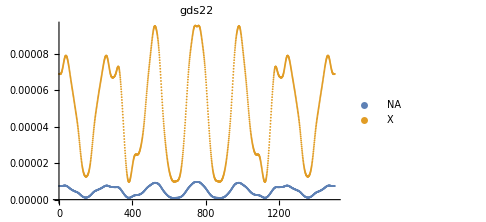
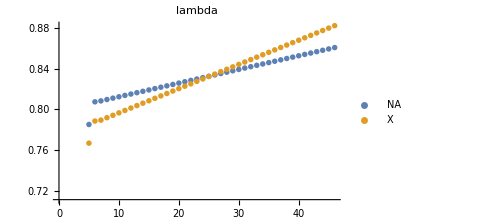
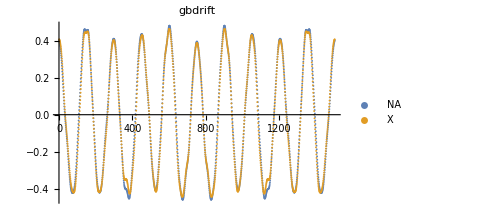
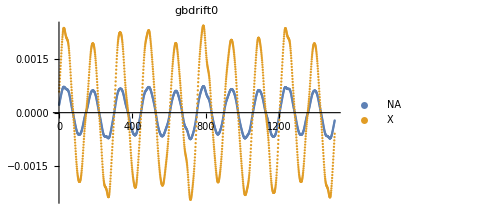
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
geomCoeff=Grid[{{ListPlot[{Import[filenameNA,{"Datasets","gradpar"}],Import[filenameX,{"Datasets","gradpar"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gradpar"],
ListPlot[{Import[filenameNA,{"Datasets","bmag"}],Import[filenameX,{"Datasets","bmag"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"bmag"]},
{ListPlot[{Import[filenameNA,{"Datasets","gds2"}],Import[filenameX,{"Datasets","gds2"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gds2"],
ListPlot[{Import[filenameNA,{"Datasets","gds21"}],Import[filenameX,{"Datasets","gds21"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gds21"]},
{ListPlot[{Import[filenameNA,{"Datasets","gds22"}],Import[filenameX,{"Datasets","gds22"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gds22"],
ListPlot[{Import[filenameNA,{"Datasets","lambda"}],Import[filenameX,{"Datasets","lambda"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"lambda"]},
{ListPlot[{Import[filenameNA,{"Datasets","gbdrift"}],Import[filenameX,{"Datasets","gbdrift"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gbdrift"],
ListPlot[{Import[filenameNA,{"Datasets","gbdrift0"}],Import[filenameX,{"Datasets","gbdrift0"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"gbdrift0"]},
{ListPlot[{Import[filenameNA,{"Datasets","cvdrift"}],Import[filenameX,{"Datasets","cvdrift"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"cvdrift"],
ListPlot[{Import[filenameNA,{"Datasets","cvdrift0"}],Import[filenameX,{"Datasets","cvdrift0"}]},PlotLegends->{"NA","X"},ImageSize->Medium,PlotLabel->"cvdrift0"]}
}]
Export["../geomCoeff"<>stell<>".pdf",geomCoeff];
```

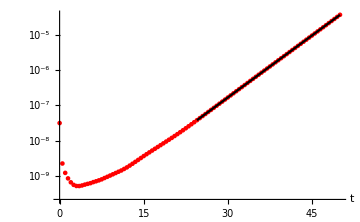
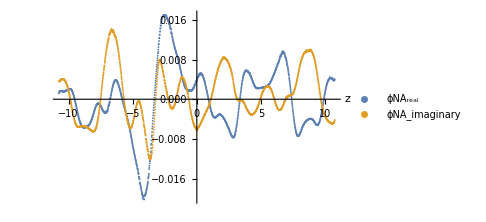
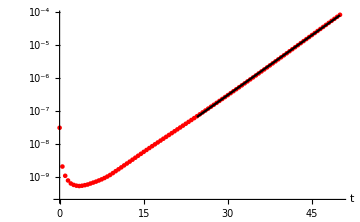
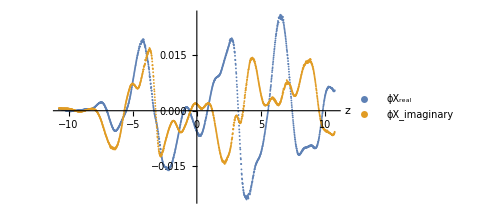
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
phiRes=Grid[{{
Show[ListLogPlot[Transpose@{timeNA,phi2NA},AxesLabel->{"t"},PlotStyle->{Red,Dashed},ImageSize->Medium],LogPlot[Exp[fitSolNA[t]],{t,timeNA[[initialT]],Last@timeNA},PlotStyle->{Black}],
Epilog->Inset[Framed[Column[{PointLegend[{Red},{"    |ϕNA|^2"}],LineLegend[{Black},{"fit γNA="<>gammaNA}]}],RoundingRadius->4],Scaled[{0.3,0.75}]]
],
ListPlot[{Transpose@{thetaNA,phiNA[[All,1]]},Transpose@{thetaNA,phiNA[[All,2]]}},PlotLegends->{"ϕNA_real","ϕNA_imaginary"},AxesLabel->{"z"},ImageSize->Medium]},
{
Show[ListLogPlot[Transpose@{timeX,phi2X},AxesLabel->{"t"},PlotStyle->{Red,Dashed},ImageSize->Medium],LogPlot[Exp[fitSolX[t]],{t,timeX[[initialT]],Last@timeX},PlotStyle->{Black}],
Epilog->Inset[Framed[Column[{PointLegend[{Red},{"    |ϕX|^2"}],LineLegend[{Black},{"fit γX="<>gammaX}]}],RoundingRadius->4],Scaled[{0.3,0.75}]]
],
ListPlot[{Transpose@{thetaX,phiX[[All,1]]},Transpose@{thetaX,phiX[[All,2]]}},PlotLegends->{"ϕX_real","ϕX_imaginary"},AxesLabel->{"z"},ImageSize->Medium]}}]
Export["../phiRes"<>stell<>".pdf",phiRes];
```